After having run ShapeAnalysis.py, evaluate this notebook to extract the curvature and other geometric measures for each of the samples. 

In “Definition of Functions” the main functions are defined, which are used to fit a spline to the outline, to compute the curvature,  and to plot various geometric measures for each sample as well as saving the data as .csv files.

In “Analysis Chick Experimental Videos” some metadata is imported for each sample, and then the analysis is run for each sample by calling “RunAll”.
Note: Creating the animated GIF takes some time, especially for samples with a lot of frames --> comment this out for faster analysis.

Afterwards, PlotsDevStage can be called to plot the geometric measures of all samples of a given developmental stage together in one plot.

In “Plots for different types of treatment”, the average of each developmental stage is plotted for the wild type, as well as for the cases where samples were perturbed mechanically and/or chemically.

```mathematica
ClearAll["`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<MaTeX`
```

```mathematica
$PlotTheme="ModStyle";
Themes`AddThemeRules["ModStyle",DefaultPlotStyle->Thread@Directive[ColorData[112,"ColorList"],Thick],Frame->True,LabelStyle->{Black,15,FontFamily->"Latin Modern Math"},AxesStyle->Black,TicksStyle->Black,Background->None,PlotRangePadding->0.01,RotateLabel->False];
```

# Definition of Functions

## Helper functions

Convert

```mathematica
(*Convert a string containing a numeric value into a number. Returns "IsString" if the conversion fails.*)
stringToNumber[s_String]:=Quiet@Check[Module[{str=StringToStream@s,n},n=Read[str,Number];Close@str;n],"IsString"]
```

```mathematica
(*Compute moving averages for each dataset in a list of datasets. The window size for each dataset is set to its length/30.*)
MovAvList[DataList_]:=Table[MovingAverage[DataList[[i]],Ceiling[Length[DataList[[i]]]/30]],{i,1,Length[DataList]}];
```

```mathematica
(*Import coordinate data from a numbered text file,clean and convert it into a list of numeric coordinate pairs.*)
ImportData[FolderCoordFiles_,kk_]:=Module[{datafile},datafile=Import[FolderCoordFiles<>IntegerString[kk,10,3]<>".txt","CSV"];
(*Replace tabs with commas and convert each line to a list of numbers*)
datafile=Table[ToExpression[StringJoin[{"{",StringReplace[datafile[[i]],"	"->","][[1]],"}"}]],{i,1,Length[datafile]}];
datafile=Table[{datafile[[i]][[1]],datafile[[i]][[2]]},{i,1,Length[datafile]}];datafile]
```

```mathematica
(*Detect and remove outlier points from a 2D dataset based on deviation of y-values from moving median filter.*)
RemoveOutliers[tab_]:=Module[{taby,movingAvg,subtractedmean,outpos,newdata},taby=Flatten[tab][[2;;;;2]];movingAvg=ArrayPad[MovingMedian[taby,5],{5-1,0},"Fixed"];
subtractedmean=(Subtract@@@Transpose[{taby,movingAvg}]);
outpos=Position[subtractedmean,x_/;Abs[x]>StandardDeviation[subtractedmean]*2.5];
Length[outpos];
outpos=Delete[tab,outpos]]
```

## Fit spline to outline and compute its curvature

```mathematica
(*Build a closed BSpline from input data. For this use to order input points. Compute signed curvature function and parameter tmin (minimizing y-coordinate). Returns spline, curvature, and tmin.*)
BSplineCurvature[data_,DegreeSpline_]:=Module[{tour,touredData,Bsfct,COM,AngleModFunc,AngleTab,DAT,DAT2,LineIntegralVal,OrientCurv,Curv,tmin,BSFunc},
(*Order points along a short tour*)
tour=FindShortestTour[data];touredData=Table[data[[tour[[2]]]][[i]],{i,1,Length[data]}];
(*Interpolate a closed B-spline*)
Bsfct=BSplineFunction[touredData[[1;;Length[touredData];;1]],SplineClosed->True,SplineDegree->Ceiling[Length[touredData]/4]];
(*Approximate COM of spline, compute angle and use these to set the orientation of the spline*)
COM=Mean[Table[Bsfct[t],{t,0,1,1/100}]];
AngleModFunc[θ_]:=If[θ<0,θ+2π,θ];
AngleTab=Evaluate[Table[AngleModFunc[ArcTan[(Bsfct[t]-COM)[[1]],(Bsfct[t]-COM)[[2]]]],{t,0,0.5,1/10}]];
DAT=Differences[AngleTab];DAT2=Table[i,{i,1,Length[DAT]}];For[ii=1,ii<Length[AngleTab],ii++,If[Abs[DAT[[ii]]]>π,If[DAT[[ii]]<0,DAT2[[ii]]=2π+DAT[[ii]],DAT2[[ii]]=DAT[[ii]]-2π],DAT2[[ii]]=DAT[[ii]]]];
LineIntegralVal=Sign[Total[DAT2]];
BSFunc[t_]:=Bsfct[LineIntegralVal*t];
(*Compute the curvature*)
Curv[t_]:=Det[{BSFunc'[t],BSFunc''[t]}]/Sqrt[BSFunc'[t].BSFunc'[t]]^3;tmin=Quiet[t/.FindMinimum[BSFunc[t][[2]],t][[2]]];{BSFunc,Curv,tmin}]
```

```mathematica
(*Import coordinate data for given frame and compute spline curvature information for frames. Returns: {coordiantes, spline, curvature,tmin}*)
RunAnalysis[FolderCoordFiles_,kk_,DegreeSpline_]:=Module[{data,ShapeData,CurvData},ShapeData=ImportData[FolderCoordFiles,kk];
CurvData=BSplineCurvature[ShapeData,DegreeSpline];{ShapeData,CurvData[[1]],CurvData[[2]],CurvData[[3]]}]
```

```mathematica
(*For a chosen dataset (row mm of TabData), run analysis (pretransition, i.e., without a transition occuring) on all frames, compute per-frame parameter shifts that best align consecutive spline parameterizations, determine
sign of curvature. Returns all relevant data*)
FullAnalysis[TabData_,mm_]:=Module[{FolderCoordFiles,FinalFrame,FullTab,FirstVal,tShiftTab,newshift,CurvSignBT,TimeStep,LengthStep,TransFrame},
(*Pull metadata for this dataset from TabData*)
FolderCoordFiles=TabData[[mm,1]]<>"/Outline_Outside_Coords/Coords_0";
FinalFrame=TabData[[mm,2]]-1;
TimeStep=TabData[[mm,3]];
LengthStep=TabData[[mm,4]];
TransFrame=TabData[[mm,5]];

(*Run analysis over all frames*)
FullTab=Table[RunAnalysis[FolderCoordFiles,kk,20],{kk,0,FinalFrame}];

(*Find initial parameter shift aligning frame 2 to frame 1. Then iteratively compute shift aligning each frame to previous one*)
FirstVal=PositionSmallest[Table[Norm[FullTab[[2]][[2]][t]-FullTab[[1]][[2]][0]],{t,0,1,1/500}]][[1]]/500;tShiftTab={0,FirstVal};For[ii = 3,ii < FinalFrame + 1,ii++, newshift=PositionSmallest[Table[Norm[FullTab[[ii]][[2]][t]-FullTab[[ii-1]][[2]][tShiftTab[[ii-1]]+0]],{t,0,1,1/500}]][[1]]/500;AppendTo[tShiftTab,newshift]];Clear[ii];
(*Curvature sign at (approx.) top of the shape for each frame*)
CurvSignBT=Table[If[FullTab[[kk]][[3]][Quiet[t/.FindMaximum[FullTab[[kk]][[2]][t][[2]],{t,0.5}][[2]]]]<0,-1,1],{kk,1,FinalFrame}];{FinalFrame,FullTab,tShiftTab,CurvSignBT,TimeStep,LengthStep,TransFrame}]
```

```mathematica
(*Compute curvature time series,identify two negative-curvature minima per frame. Smooth data, make plots and export csv files. Return key outputs.*)
ShiftedCurvatureModule[TabData_,FullTab_,FinalFrame_,tShiftTab_,mm_,MvMedNum_,TimeStep_,LengthStep_,TransFrame_]:=Module[{CorrectedCurvature,CurvTab,AvCurvTime,MovMedTab,FirstMinCurvTab,SecondMinCuvTab,NegCurvList,DiffFromSmallestCurv,DiffFromSmallestCurv2,SecondMinCuv,tab1,tab2,tab3,tab4,tab1n,tab2n,te1,te2,te3,MovMedPlotCurv,RSPosMin1,RSPosMin2,SecondMinT,LastFrameNegCurv,AvCurvTimePlot,ShiftFrame},
(*Align curvatures by (potentially) shifting arc length parameter.*)
CorrectedCurvature[t_,ii_]:=FullTab[[ii]][[3]][t+tShiftTab[[ii]]];
(*Discretize curvature over t∈[0,1.1] with Δt=0.01 for each frame*)
CurvTab=Table[Table[{t,CorrectedCurvature[t,ii]},{t,0,1.1,1/100}],{ii,1,FinalFrame,1}];

(*Mean curvature over t∈[0,1] for each frame. Apply moving median to smoothen data, use parameter MvMedNum to set window.*)
AvCurvTime=Table[Quiet@NIntegrate[CorrectedCurvature[t,ii],{t,0,1}],{ii,1,FinalFrame}];
MovMedTab=Transpose[Table[MovingMedian[CurvTab[[All,100*t+1]],MvMedNum],{t,0,1.1,1/100}]];

(*Find last frame with any negative curvature after smoothing-*)
NegCurvList={1};ii=1;While[Length[NegCurvList]>0&&ii<=FinalFrame,NegCurvList=Select[Sort[MovingMedian[MovMedTab[[ii]],1],#1[[2]]<#2[[2]]&],#1[[2]]<0&];ii++];LastFrameNegCurv=ii-1;Clear[ii];

(*Locate minima of curvature (= neck region of shape) by looking at smallest curvature value and then picking negative curvature that is approximately on the other side of the shape*)
SecondMinCuvTab=Table[NegCurvList=Select[Sort[MovingMedian[MovMedTab[[ii]],1],#1[[2]]<#2[[2]]&],#1[[2]]<0&];DiffFromSmallestCurv=Table[Min[Partition[Riffle[1-Abs[NegCurvList[[All,1]]-Mod[NegCurvList[[1,1]]+0.5,1]],Abs[NegCurvList[[All,1]]-Mod[NegCurvList[[1,1]]+0.5,1]]],2][[i]]],{i,1,Length[NegCurvList]}];
DiffFromSmallestCurv2=Flatten[Position[DiffFromSmallestCurv,_?(#<0.2&)]];(*select negative curvatures that are 0.5±0.2 away from the minimal one*)
(*If there is no such point copy the previous point to here*)
If[Length[DiffFromSmallestCurv2]>0,{SecondMinCuv=MinimalBy[NegCurvList[[DiffFromSmallestCurv2]],Last,1][[1]][[1]],SecondMinT=MinimalBy[NegCurvList[[DiffFromSmallestCurv2]],Last,1][[1]][[2]]},{SecondMinCuv=SecondMinCuv,SecondMinT=SecondMinT}](*select minimal one*),{ii,1,LastFrameNegCurv-MvMedNum+1,1}];

(*Make table of minima*)
tab1=Table[Mod[MinimalBy[MovingMedian[MovMedTab[[tt]],1],Last,1][[1,1]],1],{tt,1,LastFrameNegCurv-MvMedNum+1}];
tab2=Table[Mod[SecondMinCuvTab[[tt,1]],1],{tt,1,LastFrameNegCurv-MvMedNum+1}];tab3=Abs[Differences[tab1]];
tab4=Abs[Table[tab2[[i+1]]-tab1[[i]],{i,1,Length[tab1]-1}]];tab1n=tab1;tab2n=tab2;Table[If[tab3[[i]]<tab4[[i]],{tab1n[[i+1]]=tab1[[i+1]];tab2n[[i+1]]=tab2[[i+1]];},{tab1n[[i+1]]=tab2[[i+1]];tab2n[[i+1]]=tab1[[i+1]];tab3=Abs[Differences[tab1n]];
tab4=Abs[Table[tab2n[[i+1]]-tab1n[[i]],{i,1,Length[tab1n]-1}]];}],{i,1,Length[tab3]}];
FirstMinCurvTab=Table[CorrectedCurvature[tab2n[[ii]],ii],{ii,1,LastFrameNegCurv-MvMedNum+1}];
SecondMinCuvTab=Table[CorrectedCurvature[tab1n[[ii]],ii],{ii,1,LastFrameNegCurv-MvMedNum+1}];

(*Helper: shift time axis by transition frame if provided s. th. transition frame at origin*)
ShiftFrame[ListPlotted_]:=If[StringQ[stringToNumber[TransFrame]],Length[ListPlotted],Floor[stringToNumber[TransFrame]]];

(*---Build smoothed time-series of minima and time series, convert to SI units through provided LengthStep parameter*)
te1=MovingMedian[Table[{(ii-ShiftFrame[FirstMinCurvTab])*TimeStep,FirstMinCurvTab[[ii]]*LengthStep/50},{ii,1,Length[FirstMinCurvTab]}],3];te2=MovingMedian[Table[{(ii-ShiftFrame[FirstMinCurvTab])*TimeStep,SecondMinCuvTab[[ii]]*LengthStep/50},{ii,1,Length[SecondMinCuvTab]}],3];
te3=Table[{(ii-ShiftFrame[AvCurvTime])*TimeStep,AvCurvTime[[ii]]*LengthStep/50},{ii,1,Length[AvCurvTime]}];

(*Create plots and save them + the curvature data*)
MovMedPlotCurv=ListLinePlot[{te1,te2},FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\kappa \\text{ } [\\mu \\text{m}^{-1}]",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["\\kappa_\\text{min}^1",FontSize->12],MaTeX["\\kappa_\\text{min}^2",FontSize->12]},Top]];
AvCurvTimePlot=ListLinePlot[te3,PlotRangePadding->None,PlotRange->{Automatic,MinMax[te3[[All,2]]]*{0.9,1.1}},FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\langle\\kappa\\rangle \\text{ } [\\mu \\text{m}^{-1}]",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["\\text{Mean curvature}",FontSize->12]},Top]];
Export[TabData[[mm,1]]<>"/Plots/Data/MovMedPlotCurv.csv",{te1,te2}];
Export[TabData[[mm,1]]<>"/Plots/Data/AvCurvTimePlot.csv",te3];
Export[TabData[[mm,1]]<>"/Plots/MovMedPlotCurv.png",MovMedPlotCurv,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/AvCurvTime.png",AvCurvTimePlot,ImageResolution->600];RSPosMin1=Table[FullTab[[ii]][[2]][tab2n[[ii]]+tShiftTab[[ii]]],{ii,1,LastFrameNegCurv-MvMedNum+1}];
RSPosMin2=Table[FullTab[[ii]][[2]][tab1n[[ii]]+tShiftTab[[ii]]],{ii,1,LastFrameNegCurv-MvMedNum+1}];{CorrectedCurvature,RSPosMin1,RSPosMin2,tab1n,tab2n,LastFrameNegCurv}]
```

```mathematica
(*Creates a styled graphic marker from a primitive, with customizable colors and size.*)
marker[prim_,opts___][in_:White,out_:Black,size_:13]:=Graphics[{in,EdgeForm[{AbsoluteThickness[2],Opacity[1],out}],prim},opts,ImageSize->size];
(*Example marker: filled circle with outlined edge.*)
circle=marker@Disk[];
```

## Animated GIF of spline and shape of a single sample. Plots of geometric measures. Export of data and plots.

```mathematica
(*Generate and export a GIF and associated plots showing the evolution of shape, curvature, and geometric properties over time.*)
ExportGif[TabData_,mm_,FullTab_,tShiftTab_,RSPosMin1_,RSPosMin2_,MvMedNum_,LastFrameNegCurv_,TimeStep_,LengthStep_,TransFrame_]:=Module[{FolderImFiles,FinalFrame,prop,ImpImTab,data1,data2,data3,data4,data5,data6,data7,data8,data9,Lin,Anim,ShiftFrame,te1,te2,te3,te4,te5,te6,te7,ArcLengthAreaOverTime,ArcLengthOverAreaOverTime,AspectRatioOverTime,HeightOverTime,AbsoluteAreaOverTime},

(*Path and frame count*)
FolderImFiles=TabData[[mm,1]]<>"/Outline_Outside_Coords/0";
FinalFrame=TabData[[mm,2]]-1;

(*Import per-frame properties of shape*)
prop=Import[TabData[[mm,1]]<>"/Outline_Outside_Coords/Properties.txt","CSV"];prop=Table[ToExpression[StringJoin[{"{",StringReplace[prop[[i]],"	"->","][[1]],"}"}]],{i,1,Length[prop]}];

(*Import all .tif files with binarized shapes*)
ImpImTab=Table[Import[FolderImFiles<>IntegerString[kk-1,10,3]<>".tif"],{kk,1,FinalFrame}];

(*Center coordinates relative to COM, rotate to reference orientation, retranslate*)
data1=Table[Table[FullTab[[kk]][[1]][[i]]-({prop[[kk,1]],prop[[kk,2]]}),{i,1,Length[FullTab[[kk]][[1]]]}],{kk,1,FinalFrame}];data2=Table[data1[[kk]]/.{x_?NumericQ,y_?NumericQ}:>RotationMatrix[prop[[1,5]]/180*π].{x,y},{kk,1,FinalFrame}];
data3=Table[Table[data2[[kk]][[i]]+({prop[[kk,1]],prop[[kk,2]]}),{i,1,Length[data2[[kk]]]}],{kk,1,FinalFrame}];

data4=Table[RSPosMin1[[kk]]-({prop[[kk,1]],prop[[kk,2]]}),{kk,1,LastFrameNegCurv-MvMedNum+1}];data5=Table[data4[[kk]]/.{x_?NumericQ,y_?NumericQ}:>RotationMatrix[prop[[1,5]]/180*π].{x,y},{kk,1,LastFrameNegCurv-MvMedNum+1}];
data6=Table[data5[[kk]]+({prop[[kk,1]],prop[[kk,2]]}),{kk,1,LastFrameNegCurv-MvMedNum+1}];

data7=Table[RSPosMin2[[kk]]-({prop[[kk,1]],prop[[kk,2]]}),{kk,1,LastFrameNegCurv-MvMedNum+1}];data8=Table[data7[[kk]]/.{x_?NumericQ,y_?NumericQ}:>RotationMatrix[prop[[1,5]]/180*π].{x,y},{kk,1,LastFrameNegCurv-MvMedNum+1}];
data9=Table[data8[[kk]]+({prop[[kk,1]],prop[[kk,2]]}),{kk,1,LastFrameNegCurv-MvMedNum+1}];

(*Build per-frame composite figures combining: original image + outline points + fitted spline + markers for curvature minima and connecting line whose length corresponds to width of neck. Animate these to export as gif below*)

Anim=Animate[ImageRotate[ImageReflect[Show[{ImageReflect[ImpImTab[[tt]]],ListPlot[Join[data3[[tt]],{data3[[tt]][[1]]}],PlotStyle->{Red,Thick}],ParametricPlot[(FullTab[[tt]][[2]][tShiftTab[[tt]]+t]-{prop[[tt,1]],prop[[tt,2]]}).RotationMatrix[(-prop[[1,5]])/180*π]+{prop[[tt,1]],prop[[tt,2]]},{t,0,1}],If[tt<=LastFrameNegCurv,ListPlot[{{data6[[tt]]},{data9[[tt]]}},PlotStyle->{{Red,PointSize[0.05]},{Blue,PointSize[0.05]}}],{}],If[tt<=LastFrameNegCurv,ListLinePlot[{data6[[tt]],data9[[tt]]}],{}]}],Left],π],{tt,1,FinalFrame-MvMedNum+1,1},Bookmarks->{"start":>{tt=1},"stop":>{tt=FinalFrame-MvMedNum+1}}];

(*Helper: convert given parameter of transition frame to integer*)
ShiftFrame[ListPlotted_]:=If[StringQ[stringToNumber[TransFrame]],Length[ListPlotted],Floor[stringToNumber[TransFrame]]];

(*Construct time-series of variaous properties of the shape. Convert to SI units using TimeStep. See plots below for meaning of these.*)
te1=Table[{(ii-ShiftFrame[prop[[All,6]]])*TimeStep,(prop[[All,6]]/prop[[1,6]])[[ii]]},{ii,1,Length[prop[[All,6]]]}];te2=Table[{(ii-ShiftFrame[prop[[All,7]]])*TimeStep,(prop[[All,7]]/prop[[1,7]])[[ii]]},{ii,1,Length[prop[[All,7]]]}];te3=Table[{(ii-ShiftFrame[prop[[All,6]]])*TimeStep,(prop[[All,6]]/Sqrt[prop[[All,7]]])[[ii]]},{ii,1,Length[prop[[All,6]]]}];te4=Table[{(ii-ShiftFrame[prop[[All,6]]])*TimeStep,(2π)/Sqrt[π]},{ii,1,Length[prop[[All,6]]]}];
te5=Table[{(ii-ShiftFrame[prop[[All,3]]])*TimeStep,(prop[[All,3]]/prop[[All,4]])[[ii]]},{ii,1,Length[prop[[All,3]]]}];
te6=Table[{(ii-ShiftFrame[prop[[All,3]]])*TimeStep,(prop[[All,4]])[[ii]]},{ii,1,Length[prop[[All,3]]]}];
te7=Table[{(ii-ShiftFrame[prop[[All,3]]])*TimeStep,(prop[[All,7]])[[ii]]},{ii,1,Length[prop[[All,3]]]}];

(*Plot this data*)
ArcLengthAreaOverTime=ListLinePlot[{te1,te2},FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],MaTeX[" ",FontSize->15]},PlotLegends->Placed[{MaTeX["L/L_0 \\text{ norm. arc-length}",FontSize->12],MaTeX["A/A_0 \\text{ norm. area}",FontSize->12]},Top]];
ArcLengthOverAreaOverTime=ListLinePlot[{te3,te4},FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{L}{\\sqrt{A}}",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["\\text{Arc-length over sqrt of area}",FontSize->12]},Top]];
AspectRatioOverTime=ListLinePlot[te5,FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{W}{H}",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["\\text{Width/Height}",FontSize->12]},Top]];
HeightOverTime=ListLinePlot[te6,FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["H \\text{ } [\\mu \\text{m}]",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["\\text{Height}",FontSize->12]},Top]];
AbsoluteAreaOverTime=ListLinePlot[te7,FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["A \\text{ } [\\mu \\text{m}^2]",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["\\text{Area}",FontSize->12]},Top]];

(*Export plots, animation, and data used for plots.*)
Export[TabData[[mm,1]]<>"/ImPointSpline_Comp.gif",Anim];
Export[TabData[[mm,1]]<>"/Plots/Data/ArcLengthAreaOverTime.csv",{te1,te2}];
Export[TabData[[mm,1]]<>"/Plots/Data/ArcLengthOverAreaOverTime.csv",{te3,te4}];
Export[TabData[[mm,1]]<>"/Plots/Data/AspectRatioOverTime.csv",te5];
Export[TabData[[mm,1]]<>"/Plots/Data/HeightOverTime.csv",te6];
Export[TabData[[mm,1]]<>"/Plots/Data/AbsoluteAreaOverTime.csv",te7];
Export[TabData[[mm,1]]<>"/Plots/ArcLengthAreaOverTime.png",ArcLengthAreaOverTime,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/ArcLengthOverAreaOverTime.png",ArcLengthOverAreaOverTime,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/AspectRatioOverTime.png",AspectRatioOverTime,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/HeightOverTime.png",HeightOverTime,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/AbsoluteAreaOverTime.png",AbsoluteAreaOverTime,ImageResolution->600];]
```

```mathematica
(*Quantify geometric measures from the spline over time: 
 
 - Relative arc-length and area (normalized by frame 1)
- L/√A vs.circle reference
- Relative distances from neck-center line to top/bottom extreme
- Relative areas above/below the neck-center line
- Neck width (distance between curvature minima) 

Exports CSVs and PNG plots for all metrics.*)

QuantifyModule[TabData_,FullTab_,tShiftTab_,FinalFrame_,RSPosMin1_,RSPosMin2_,tab1n_,tab2n_,mm_,MvMedNum_,LastFrameNegCurv_,TimeStep_,LengthStep_,TransFrame_]:=Module[{bspline,arclength,area,ShiftFrame,RelLengthAreaPlot,LenAreaRatioPlot,yMaxVal,yMinVal,DisTop,DisBot,DistTopBotPlot,trange1,trange2,gt1,gt2,ar1,area1,ar2,area2,AreaTopBotPlot,LengthNeckPlot,te1,te2,te3,te4,te5,te6,te7,te8,te9},bspline[t_,tt_]:=FullTab[[tt]][[2]][tShiftTab[[tt]]+t];

(*area and arc-length*)
arclength[tt_]:=NIntegrate[Sqrt[D[bspline[t,tt],t].D[bspline[t,tt],t]],{t,0,1}];
area[tt_]:=-NIntegrate[(D[bspline[t,tt],t]).{1,0}*(bspline[t,tt]).{0,1},{t,0,1}];
ShiftFrame[LengthListPlotted_]:=If[StringQ[stringToNumber[TransFrame]],LengthListPlotted,Floor[stringToNumber[TransFrame]]];
te1=Table[{(ii-ShiftFrame[FinalFrame])*TimeStep,arclength[ii]/arclength[1]},{ii,1,FinalFrame}];te2=Table[{(ii-ShiftFrame[FinalFrame])*TimeStep,area[ii]/area[1]},{ii,1,FinalFrame}];RelLengthAreaPlot=ListLinePlot[{te1,te2},FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],MaTeX[" ",FontSize->15]},PlotLegends->Placed[{MaTeX["L/L_0 \\text{ norm. arc-length}",FontSize->12],MaTeX["\\frac{A}{A_0} \\text{ norm. area}",FontSize->12]},Top]];

(*Length/Sqrt[Area] and comparison with circle*)
te3=Table[{(ii-ShiftFrame[FinalFrame])*TimeStep,arclength[ii]/Sqrt[area[ii]]},{ii,1,FinalFrame}];te4=Table[{(ii-ShiftFrame[FinalFrame])*TimeStep,(2π)/Sqrt[π]},{ii,1,FinalFrame}];LenAreaRatioPlot=ListLinePlot[{te3,te4},FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{L}{\\sqrt{A}}",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["\\text{Arc-length over sqrt of area}",FontSize->12]},Top]];

(*Distance from center of neck line to top and bottom*)
yMaxVal[tt_]:=Quiet@FindMaximum[FullTab[[tt]][[2]][tShiftTab[[tt]]+t][[2]],{t,0,1}];
yMinVal[tt_]:=Quiet@FindMinimum[FullTab[[tt]][[2]][tShiftTab[[tt]]+t][[2]],{t,0,1}];
DisTop[tt_]:=Norm[(RSPosMin1[[tt]]+RSPosMin2[[tt]])/2-FullTab[[tt]][[2]][tShiftTab[[tt]]+t/.yMaxVal[tt][[2]]]];
DisBot[tt_]:=Norm[(RSPosMin1[[tt]]+RSPosMin2[[tt]])/2-FullTab[[tt]][[2]][tShiftTab[[tt]]+t/.yMinVal[tt][[2]]]];
te5=Table[{(ii-ShiftFrame[LastFrameNegCurv-MvMedNum+1])*TimeStep,DisTop[ii]/(DisTop[ii]+DisBot[ii])},{ii,1,LastFrameNegCurv-MvMedNum+1}];te6=Table[{(ii-ShiftFrame[LastFrameNegCurv-MvMedNum+1])*TimeStep,DisBot[ii]/(DisTop[ii]+DisBot[ii])},{ii,1,LastFrameNegCurv-MvMedNum+1}];
DistTopBotPlot=ListLinePlot[{te5,te6},FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{d_i}{d}",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["d_1/d \\text{ Rel. dist. top-neck}",FontSize->12],MaTeX["d_2/d \\text{ Rel. dist. bottom-neck}",FontSize->12]},Top]];

(*Area above and below line*)
trange1[tt_]:={tab1n[[tt]],If[tab2n[[tt]]>tab1n[[tt]],tab2n[[tt]],1+tab2n[[tt]]]};
trange2[tt_]:={trange1[tt][[2]]-1,trange1[tt][[1]]};gt1=Table[BSplineFunction[Table[FullTab[[tt]][[2]][tShiftTab[[tt]]+t],Evaluate[Join[{t},trange1[tt],{1/1000}]]],SplineClosed->True,SplineDegree->3],{tt,1,LastFrameNegCurv-MvMedNum+1}];
gt2=Table[BSplineFunction[Table[FullTab[[tt]][[2]][tShiftTab[[tt]]+t],Evaluate[Join[{t},trange2[tt],{1/1000}]]],SplineClosed->True,SplineDegree->3],{tt,1,LastFrameNegCurv-MvMedNum+1}];
ar1[t_?NumericQ,tt_]:=((gt1[[tt]])'[t])[[1]]*((gt1[[tt]])[t])[[2]];area1[tt_]:=-Quiet@NIntegrate[ar1[t,tt],{t,0,1}];
ar2[t_?NumericQ,tt_]:=((gt2[[tt]])'[t])[[1]]*((gt2[[tt]])[t])[[2]];area2[tt_]:=-Quiet@NIntegrate[ar2[t,tt],{t,0,1}];
te7=Table[{(ii-ShiftFrame[LastFrameNegCurv-MvMedNum+1])*TimeStep,area1[ii]/area[ii]},{ii,1,LastFrameNegCurv-MvMedNum+1}];te8=Table[{(ii-ShiftFrame[LastFrameNegCurv-MvMedNum+1])*TimeStep,area2[ii]/area[ii]},{ii,1,LastFrameNegCurv-MvMedNum+1}];AreaTopBotPlot=ListLinePlot[{te7,te8},FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{A_i}{A}",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["A_1/A \\text{Rel. area top-neck}",FontSize->12],MaTeX["A_2/A \\text{Rel. area bottom-neck}",FontSize->12]},Top]];

(*Length neck*)
te9=Table[{(ii-ShiftFrame[LastFrameNegCurv-MvMedNum+1])*TimeStep,Norm[RSPosMin1[[ii]]-RSPosMin2[[ii]]]*50/LengthStep},{ii,1,LastFrameNegCurv-MvMedNum+1}];
LengthNeckPlot=ListLinePlot[te9,FrameLabel->{MaTeX["\\text{t }[\\text{min}]",FontSize->15],Rotate[MaTeX["d_n \\text{ } [\\mu \\text{m}]",FontSize->15],-Pi/2]},PlotLegends->Placed[{MaTeX["\\text{Width neck}",FontSize->12]},Top]];
Export[TabData[[mm,1]]<>"/Plots/Data/RelLengthAreaPlot.csv",{te1,te2}];
Export[TabData[[mm,1]]<>"/Plots/Data/LenAreaRatioPlot.csv",{te3,te4}];
Export[TabData[[mm,1]]<>"/Plots/Data/DistTopBotPlot.csv",{te5,te6}];
Export[TabData[[mm,1]]<>"/Plots/Data/AreaTopBotPlot.csv",{te7,te8}];
Export[TabData[[mm,1]]<>"/Plots/Data/LengthNeckPlot.csv",te9];
Export[TabData[[mm,1]]<>"/Plots/RelLengthAreaPlot.png",RelLengthAreaPlot,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/LenAreaRatioPlot.png",LenAreaRatioPlot,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/DistTopBotPlot.png",DistTopBotPlot,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/AreaTopBotPlot.png",AreaTopBotPlot,ImageResolution->600];
Export[TabData[[mm,1]]<>"/Plots/LengthNeckPlot.png",LengthNeckPlot,ImageResolution->600];]
```

```mathematica
(*Export points of outline, data of bspline and data of curvature to .txt files.*)
ExportModule[TabData_,FullTab_,FinalFrame_,CorrectedCurvature_,tShiftTab_,mm_]:=Module[{Folder,pts,BSplTab,CurTab},pts=Table[Flatten[FullTab[[tt]][[1]]],{tt,1,FinalFrame}];
BSplTab=Table[Flatten[Table[FullTab[[tt]][[2]][tShiftTab[[tt]]+t],{t,0,1,1/200}]],{tt,1,FinalFrame}];
CurTab=Table[Flatten[Table[{N[t],CorrectedCurvature[t,tt]},{t,0,1,1/200}]],{tt,1,FinalFrame}];Export[TabData[[mm,1]]<>"/Plots/Data/Points_All.txt",pts,"CSV"];Export[TabData[[mm,1]]<>"/Plots/Data/BSpline_All.txt",BSplTab,"CSV"];Export[TabData[[mm,1]]<>"/Plots/Data/Curvature_All.txt",CurTab,"CSV"];]
```

## Main run function

```mathematica
(*Import metadata from excel sheet and align it with TabData rows. For each dataset: extract time step & length scale (to convert to physical units), transition frame (to align plots), and type (wild type or which chemical/mechanical perturbation).*)
ModuleImportScaleData[TabData_,excelsheetname_]:=Module[{excelsheet,CleanNameData,CleanNameList,indexlist,indexlist2,timesteplist,lengthscalelist,transitionframelist,typelist,storedata},excelsheet=Import[excelsheetname,{"Dataset",1},"HeaderLines"->1];CleanNameData=DeleteCases[excelsheet[All,2],excelsheet[200,2]];
CleanNameList=Normal[CleanNameData][[2;;]];indexlist=Quiet@Table[Position[StringContainsQ[TabData[[All,1]],ToString[CleanNameList[[i]]]<>"-"],True]/.{}->-100,{i,1,Length[CleanNameList]}];indexlist2=Sort[DeleteCases[Partition[Riffle[Table[i,{i,1,Length[indexlist]}],Flatten[indexlist]],2],{_,_?Negative}],#1[[2]]<#2[[2]]&];(*first is index of excel,second of TabData*)
timesteplist=Normal[DeleteCases[excelsheet[All,3],excelsheet[200,2]]][[2;;]];
lengthscalelist=Normal[DeleteCases[excelsheet[All,4],excelsheet[200,2]]][[2;;]];
transitionframelist=Normal[DeleteCases[excelsheet[All,6],excelsheet[200,2]]][[2;;]];
typelist=Normal[DeleteCases[excelsheet[All,5],excelsheet[200,2]]][[2;;]];
storedata=Table[{timesteplist[[indexlist2[[i,1]]]],lengthscalelist[[indexlist2[[i,1]]]],transitionframelist[[indexlist2[[i,1]]]],typelist[[indexlist2[[i,1]]]]},{i,1,Length[indexlist2]}]]
```

```mathematica
(*Run analysis for all samples.*)
RunAll[TabData_,ii_,MvMedNum_]:=Module[{FinalFrame,FullTab,tShiftTab,CurvSignBT,TimeStep,LengthStep,TransFrame,CorrectedCurvature,RSPosMin1,RSPosMin2,tab1n,tab2n,LastFrameNegCurv},{FinalFrame,FullTab,tShiftTab,CurvSignBT,TimeStep,LengthStep,TransFrame}=FullAnalysis[TabData,ii];{CorrectedCurvature,RSPosMin1,RSPosMin2,tab1n,tab2n,LastFrameNegCurv}=ShiftedCurvatureModule[TabData,FullTab,FinalFrame,tShiftTab,ii,MvMedNum,TimeStep,LengthStep,TransFrame];
ExportGif[TabData,ii,FullTab,tShiftTab,RSPosMin1,RSPosMin2,MvMedNum,LastFrameNegCurv,TimeStep,LengthStep,TransFrame];QuantifyModule[TabData,FullTab,tShiftTab,FinalFrame,RSPosMin1,RSPosMin2,tab1n,tab2n,ii,MvMedNum,LastFrameNegCurv,TimeStep,LengthStep,TransFrame];ExportModule[TabData,FullTab,FinalFrame,CorrectedCurvature,tShiftTab,ii];]
```

## Plot and export of several samples & averages for given developmental stage

```mathematica
(*Combining plots of geometric measures of all samples of given developmental stage into a single figure. Combines data plotted already above for each sample seperately into a single plot for each stage and plots saved in respective folder.*)
PlotsDevStage[TabData_,TabDevStage_,mm_]:=Module[{IndDevStage,LegendList,ImpPlotData,MovMedPlotCurv1,MovMedPlotCurv2,AvCurvTimePlot,AspectRatioOverTime,RelLengthAreaPlot1,RelLengthAreaPlot2,LenAreaRatioPlot,DistTopBotPlot1,DistTopBotPlot2,AreaTopBotPlot1,AreaTopBotPlot2,LengthNeckPlot,HeightPlot,AreaPlot},IndDevStage=Table[Flatten@Position[StringContainsQ[TabData[[All,1]],ToString[TabDevStage[[i]]]],True],{i,1,Length[TabDevStage]}][[mm]];LegendList=Table[StringDrop[StringCases[TabData[[i,1]],"20"~~__~~"-"~~__~~"-"][[1]],-1],{i,IndDevStage[[1]],IndDevStage[[-1]]}];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/MovMedPlotCurv.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];
MovMedPlotCurv1=ListLinePlot[Flatten[ImpPlotData,1][[1;;;;2]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\kappa \\text{ } [\\mu \\text{m}^{-1}]",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Minimal curvature left}",FontSize->20],PlotLegends->LegendList];
MovMedPlotCurv2=ListLinePlot[Flatten[ImpPlotData,1][[2;;;;2]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\kappa \\text{ } [\\mu \\text{m}^{-1}]",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Minimal curvature right}",FontSize->20],PlotLegends->LegendList];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/AvCurvTimePlot.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];
AvCurvTimePlot=ListLinePlot[MovAvList@ImpPlotData,FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\langle\\kappa\\rangle \\text{ } [\\mu \\text{m}^{-1}]",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Average curvature}",FontSize->20],PlotLegends->LegendList,PlotRangePadding->None,PlotRange->{Automatic,MinMax[ImpPlotData[[All,All,2]]]*{0.9,1.1}}];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/AspectRatioOverTime.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];AspectRatioOverTime=ListLinePlot[MovAvList@ImpPlotData,FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{W}{H}",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Aspect ratio width/height}",FontSize->20],PlotLegends->LegendList];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/RelLengthAreaPlot.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];RelLengthAreaPlot1=ListLinePlot[MovAvList@Flatten[ImpPlotData,1][[1;;;;2]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],MaTeX[" ",FontSize->15]},PlotLabel->MaTeX["\\text{Normalized arc-length}",FontSize->20],PlotLegends->LegendList];
RelLengthAreaPlot2=ListLinePlot[MovAvList@Flatten[ImpPlotData,1][[2;;;;2]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],MaTeX[" ",FontSize->15]},PlotLabel->MaTeX["\\text{Normalized area}",FontSize->20],PlotLegends->LegendList];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/LenAreaRatioPlot.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];LenAreaRatioPlot=Show[ListLinePlot[MovAvList@Join[Flatten[ImpPlotData,1][[1;;;;2]],Flatten[ImpPlotData,1][[2;;;;2]]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{L}{\\sqrt{A}}",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Arclength}/\\sqrt{\\text{area}}",FontSize->20],PlotLegends->LegendList]];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/DistTopBotPlot.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];DistTopBotPlot1=ListLinePlot[MovAvList@Flatten[ImpPlotData,1][[1;;;;2]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{d_i}{d}",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Relative distance from neck to top}",FontSize->20],PlotLegends->LegendList];
DistTopBotPlot2=ListLinePlot[MovAvList@Flatten[ImpPlotData,1][[2;;;;2]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{d_i}{d}",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Relative distance from neck to bottom}",FontSize->20],PlotLegends->LegendList];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/AreaTopBotPlot.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];AreaTopBotPlot1=ListLinePlot[MovAvList@Flatten[ImpPlotData,1][[1;;;;2]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{A_i}{A}",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Relative area above neck}",FontSize->20],PlotLegends->LegendList];
AreaTopBotPlot2=ListLinePlot[MovAvList@Flatten[ImpPlotData,1][[2;;;;2]],FrameLabel->{MaTeX["t \\text{ }[\\text{min}]",FontSize->15],Rotate[MaTeX["\\frac{A_i}{A}",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Relative area below neck}",FontSize->20],PlotLegends->LegendList];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/LengthNeckPlot.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];LengthNeckPlot=ListLinePlot[MovAvList@ImpPlotData,FrameLabel->{MaTeX["\\text{t }[\\text{min}]",FontSize->15],Rotate[MaTeX["d_n \\text{ } [\\mu \\text{m}]",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Width of neck}",FontSize->20],PlotLegends->LegendList];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/HeightOverTime.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];HeightPlot=ListLinePlot[MovAvList@ImpPlotData,FrameLabel->{MaTeX["\\text{t }[\\text{min}]",FontSize->15],Rotate[MaTeX["H \\text{ } [\\mu \\text{m}]",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Height}",FontSize->20],PlotLegends->LegendList];

ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/AbsoluteAreaOverTime.csv"]],{i,IndDevStage[[1]],IndDevStage[[-1]]}];AreaPlot=ListLinePlot[MovAvList@ImpPlotData,FrameLabel->{MaTeX["\\text{t }[\\text{min}]",FontSize->15],Rotate[MaTeX["A \\text{ } [\\mu \\text{m}^2]",FontSize->15],-Pi/2]},PlotLabel->MaTeX["\\text{Area}",FontSize->20],PlotLegends->LegendList];

Export[TabDevStage[[mm]]<>"/Plots/MovMedPlotCurv1.png",MovMedPlotCurv1,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/MovMedPlotCurv2.png",MovMedPlotCurv2,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/AvCurvTimePlot.png",AvCurvTimePlot,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/AspectRatioOverTime.png",AspectRatioOverTime,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/RelLengthAreaPlot1.png",RelLengthAreaPlot1,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/RelLengthAreaPlot2.png",RelLengthAreaPlot2,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/LenAreaRatioPlot.png",LenAreaRatioPlot,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/DistTopBotPlot1.png",DistTopBotPlot1,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/DistTopBotPlot2.png",DistTopBotPlot2,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/AreaTopBotPlot1.png",AreaTopBotPlot1,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/AreaTopBotPlot2.png",AreaTopBotPlot2,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/LengthNeckPlot.png",LengthNeckPlot,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/Height.png",HeightPlot,ImageResolution->600];
Export[TabDevStage[[mm]]<>"/Plots/AbsoluteArea.png",AreaPlot,ImageResolution->600];]
```

```mathematica
(*Build interpolating functions for each dataset. Split into two groups (ones where transition occured vs. ones where it didn't) by considering if domain of curve crosses (shifted) time axis origin. For each group:

 - Sample all interpolated functions on 5-unit grid over common domain
- Collect all valid values at each x
- Compute median and median deviation across functions + record how many functions contributed at each x

Return data for both groups.*)
PerformAverageSamplesModule[datalist_]:=Module[{interlist,domainlist,indlisttrans,indlistno,interlisttrans,domainlisttrans,interlistno,domainlistno,avtabtrans,avtabno,transallvaltab1,avtab1,meddevtab1,transallvaltab2,avtab2,meddevtab2},interlist=Table[Interpolation[datalist[[ii]]],{ii,1,Length[datalist]}];
domainlist=Table[interlist[[ii]]["Domain"][[1]],{ii,1,Length[datalist]}];
indlisttrans=Flatten[Position[domainlist[[All,2]],_?(#>0&)]];
indlistno=Flatten[Position[domainlist[[All,2]],_?(#<=0&)]];
interlisttrans=interlist[[indlisttrans]];
domainlisttrans=domainlist[[indlisttrans]];
interlistno=interlist[[indlistno]];
domainlistno=domainlist[[indlistno]];
avMod[intlist_,domainlist_,xval_]:=Module[{xvalind,aa,l},xvalind=(xval-Min[Flatten[domainlist]])/5+1;
Clear[ii];l={};For[ii=1,ii<Length[intlist]+1,ii++,If[domainlist[[ii]][[1]]<=xval<=domainlist[[ii]][[2]],AppendTo[l,intlist[[ii]][xval]]]];l];
avtabtrans=Table[{xval,avMod[interlisttrans,domainlisttrans,xval]},{xval,Min[Flatten@domainlisttrans],Max[Flatten@domainlisttrans],5}];If[Length[domainlistno]>0,
avtabno=Table[{xval,avMod[interlistno,domainlistno,xval]},{xval,Min[Flatten@domainlistno],Max[Flatten@domainlistno],5}];,avtabno={};];transallvaltab1=Table[{xval,avMod[interlisttrans,domainlisttrans,xval]},{xval,Min[Flatten[domainlisttrans]],Max[Flatten[domainlisttrans]],5}];
avtab1=Table[{transallvaltab1[[ii,1]],Median[transallvaltab1[[ii,2]]],Length[transallvaltab1[[ii,2]]]},{ii,1,Length[transallvaltab1]}];
meddevtab1=Table[{transallvaltab1[[ii,1]],MedianDeviation[transallvaltab1[[ii,2]]]},{ii,1,Length[transallvaltab1]}];
If[Length[domainlistno]>0,transallvaltab2=Table[{xval,avMod[interlistno,domainlistno,xval]},{xval,Min[Flatten[domainlistno]],Max[Flatten[domainlistno]],5}];,transallvaltab2={};];
avtab2=Table[{transallvaltab2[[ii,1]],Median[transallvaltab2[[ii,2]]],Length[transallvaltab2[[ii,2]]]},{ii,1,Length[transallvaltab2]}];
meddevtab2=Table[{transallvaltab2[[ii,1]],MedianDeviation[transallvaltab2[[ii,2]]]},{ii,1,Length[transallvaltab2]}];{avtab1,meddevtab1,avtab2,meddevtab2,Length[indlisttrans],Length[indlistno],domainlisttrans,domainlistno}]
```

```mathematica
(*Given average and deviation, create data Average ± Devation to be plotted.*)
VariationFunc[avdata_,devdata_]:={Partition[Riffle[avdata[[All,1]],avdata[[All,2]]+devdata[[All,2]]],2],Partition[Riffle[avdata[[All,1]],avdata[[All,2]]-devdata[[All,2]]],2]}
```

```mathematica
(*For given developmental stage (indexed by mm), get datasets from TabData whose names contain that stage tag as well as a SelectString that determine if chemical/mechanical perturbation (e.g. "Yes" for wild type samples). Any indices in IgnoreCases are ignored. Load per-frame properties and curvature, remove outliers, rescale amplitudes by physical width, and compute median profiles (and median deviations) across datasets using PerformAverageSamplesModule.*)
AverageSampleWTOnly[TabData_,TabDevStage_,mm_,SelectString_,IgnoreCases_:{}]:=Module[{IndDevStage,LegendList,widthdatalist,propdata,ImpPlotData,MinCurv1Tab,MinCurv1NoOuty,MinCurv1NoOut,MinCurv2Tab,MinCurv2NoOuty,MinCurv2NoOut,widthTab,widthTabNoOuty,widthTabNoOut,heightTab,heightTabNoOuty,heightTabNoOut,areaTab,areaTabNoOuty,areaTabNoOut,aspTab,aspTabNoOuty,aspTabNoOut,lenareTab,lenareTabNoOuty,lenareTabNoOut},IndDevStage=Table[DeleteElements[Flatten@Position[MapThread[And,{StringContainsQ[TabData[[All,1]],ToString[TabDevStage[[i]]]],StringContainsQ[TabData[[All,6]],SelectString]}],True],IgnoreCases],{i,1,Length[TabDevStage]}][[mm]];LegendList=Table[StringDrop[StringCases[TabData[[i,1]],"20"~~__~~"-"~~__~~"-"][[1]],-1],{i,IndDevStage}];
widthdatalist=Table[propdata=Import[TabData[[ii,1]]<>"/Outline_Outside_Coords/Properties.txt","CSV"];
propdata=Table[ToExpression[StringJoin[{"{",StringReplace[propdata[[i]],"	"->","][[1]],"}"}]],{i,1,Length[propdata]}];propdata[[All,3]]*50/TabData[[ii,4]],{ii,IndDevStage}];
ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/MovMedPlotCurv.csv"]],{i,IndDevStage}];
MinCurv1Tab=Flatten[ImpPlotData,1][[1;;;;2]];
MinCurv1NoOuty=Table[RemoveOutliers[MinCurv1Tab[[ii]]],{ii,1,Length[MinCurv1Tab]}];
MinCurv1NoOut=Table[Partition[Riffle[MinCurv1NoOuty[[ii]][[All,1]],MinCurv1NoOuty[[ii]][[All,2]]],2],{ii,1,Length[MinCurv1Tab]}];
MinCurv2Tab=Flatten[ImpPlotData,1][[2;;;;2]];
MinCurv2NoOuty=Table[RemoveOutliers[MinCurv2Tab[[ii]]],{ii,1,Length[MinCurv2Tab]}];
MinCurv2NoOut=Table[Partition[Riffle[MinCurv2NoOuty[[ii]][[All,1]],MinCurv2NoOuty[[ii]][[All,2]]],2],{ii,1,Length[MinCurv2Tab]}];
ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/LengthNeckPlot.csv"]],{i,IndDevStage}];
widthTab=ImpPlotData;
widthTabNoOuty=Table[RemoveOutliers[widthTab[[ii]]],{ii,1,Length[widthTab]}];
widthTabNoOut=Table[Partition[Riffle[widthTabNoOuty[[ii]][[All,1]],widthTabNoOuty[[ii]][[All,2]]],2],{ii,1,Length[widthTab]}];
ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/LengthNeckPlot.csv"]],{i,IndDevStage}];
widthTab=ImpPlotData;
widthTabNoOuty=Table[RemoveOutliers[widthTab[[ii]]],{ii,1,Length[widthTab]}];
widthTabNoOut=Table[Partition[Riffle[widthTabNoOuty[[ii]][[All,1]],widthTabNoOuty[[ii]][[All,2]]],2],{ii,1,Length[widthTab]}];
ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/HeightOverTime.csv"]],{i,IndDevStage}];
heightTab=ImpPlotData;
heightTabNoOuty=Table[RemoveOutliers[heightTab[[ii]]],{ii,1,Length[heightTab]}];
heightTabNoOut=Table[Partition[Riffle[heightTabNoOuty[[ii]][[All,1]],heightTabNoOuty[[ii]][[All,2]]],2],{ii,1,Length[heightTab]}];
ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/AbsoluteAreaOverTime.csv"]],{i,IndDevStage}];
areaTab=ImpPlotData;
areaTabNoOuty=Table[RemoveOutliers[areaTab[[ii]]],{ii,1,Length[areaTab]}];
areaTabNoOut=Table[Partition[Riffle[areaTabNoOuty[[ii]][[All,1]],areaTabNoOuty[[ii]][[All,2]]],2],{ii,1,Length[areaTab]}];
ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/AspectRatioOverTime.csv"]],{i,IndDevStage}];
aspTab=ImpPlotData;
aspTabNoOuty=Table[RemoveOutliers[aspTab[[ii]]],{ii,1,Length[aspTab]}];
aspTabNoOut=Table[Partition[Riffle[aspTabNoOuty[[ii]][[All,1]],aspTabNoOuty[[ii]][[All,2]]],2],{ii,1,Length[aspTab]}];
ImpPlotData=Table[ToExpression[Import[TabData[[i,1]]<>"/Plots/Data/ArcLengthOverAreaOverTime.csv"][[1]]],{i,IndDevStage}];
lenareTab=ImpPlotData;
lenareTabNoOuty=Table[RemoveOutliers[lenareTab[[ii]]],{ii,1,Length[lenareTab]}];
lenareTabNoOut=Table[Partition[Riffle[lenareTabNoOuty[[ii]][[All,1]],lenareTabNoOuty[[ii]][[All,2]]],2],{ii,1,Length[lenareTab]}];
{PerformAverageSamplesModule[Join[MinCurv1NoOut,MinCurv2NoOut]],PerformAverageSamplesModule[widthTabNoOut],PerformAverageSamplesModule[heightTabNoOut],PerformAverageSamplesModule[areaTabNoOut],PerformAverageSamplesModule[aspTabNoOut],PerformAverageSamplesModule[lenareTabNoOut]}]
```

# Analysis Chick Experimental Videos

```mathematica
(*Table of developmental stages to be considered*)
TabDevStage={"Chick_E3.5_anterior","Chick_E3.5_posterior","Chick_E3.75_anterior","Chick_E3.75_posterior","Chick_E4.0_anterior","Chick_E4.0_posterior"};
```

```mathematica
(*Import data created from python file as well as metadata saved in Metadata.xlsx file (e.g., conversion of time and length scales, if any mechanical/chemical perturbation has been performed, ...)*)
TabData = Transpose[Import["list_data.csv","CSV"]];
TabData =Partition[Riffle[StringDelete[StringDelete[TabData[[All,1]],NotebookDirectory[]],".avi"],TabData[[All,2]]],2];
storedata=ModuleImportScaleData[TabData,"Metadata.xlsx"];
TabData =Transpose@Join[Transpose@TabData,Transpose@storedata];
```

```mathematica
(*Run analysis for all samples. Saves data of spline + curvature as well as plots of geometric measure for each sample in the respective folder. Saves also GIF showing how well the spline fits the shape as well as how well the neck is identified. Prints Error at XX if there is a problem with sample XX*)
Clear[z];Monitor[Table[If[FileType[TabData[[jj,1]]<>"/Plots"]==None,z=Quiet[Check[RunAll[TabData,jj,1],err]],z=1];If[z===err,"Error at " <> ToString[jj],jj],{jj,1,Length[TabData]}],jj]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130}

```mathematica
(*Make plots for each developmental stage.*)
Monitor[Table[z=Quiet@Check[PlotsDevStage[TabData,TabDevStage,jj],err];If[z===err,"Error at " <> ToString[jj],jj],{jj,1,Length[TabDevStage]}],jj]
```

{1,2,3,4,5,6}

# Plots for different types of treatment

## Wild type

```mathematica
(*TypeString defines the kind of mechanical/chemical perturbation performed on the sample that is recorded in the excel sheet.*)
TypeString="Yes";
```

### Width

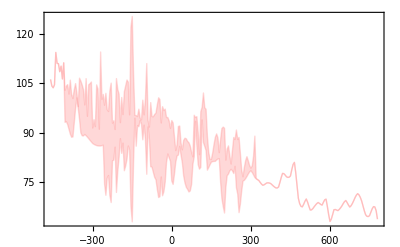
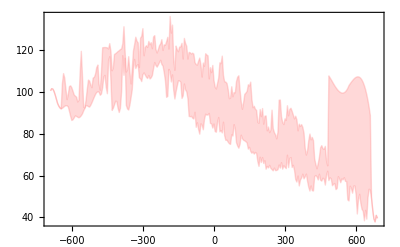
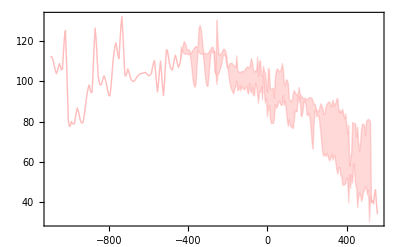
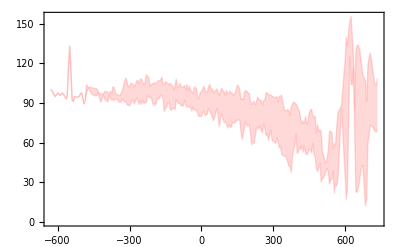
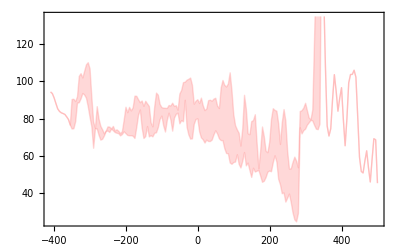
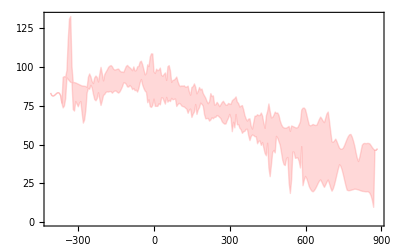

```mathematica
AllSamplWidthAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[2]],{mm,1,6}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplWidthAvTab[[ii]][[1]],AllSamplWidthAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplWidthAvTab]}]
```

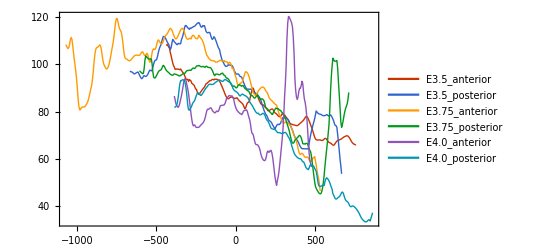

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplWidthAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Width/Width_"<>ToString[TabDevStage[[i]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplWidthAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplWidthAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,Length[TabDevStage]}];
```

### Height

```mathematica
AllSamplHeightAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[3]],{mm,1,6}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplHeightAvTab[[ii]][[1]],AllSamplHeightAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplHeightAvTab]}];
```

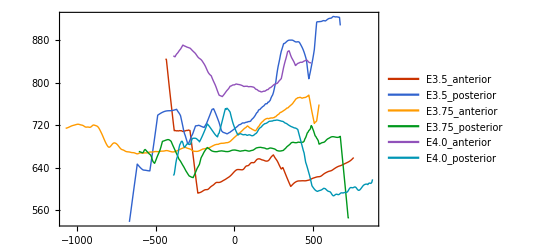

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplHeightAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Height/Height_"<>ToString[TabDevStage[[i]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplHeightAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplHeightAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,Length[TabDevStage]}];
```

### Area

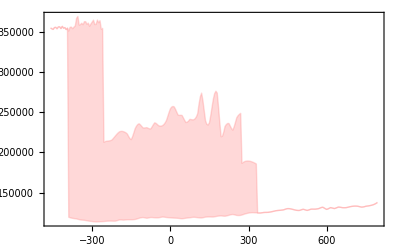
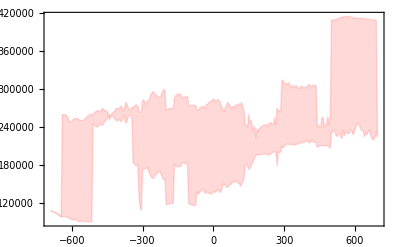
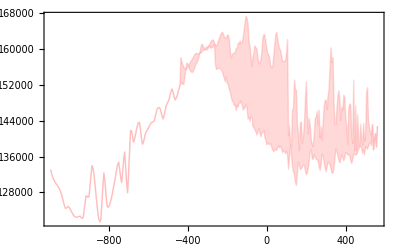
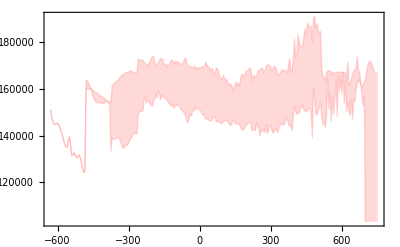
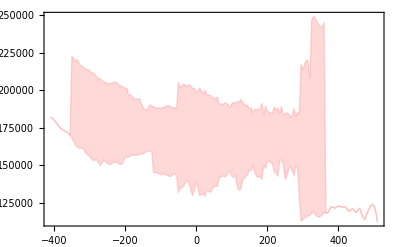
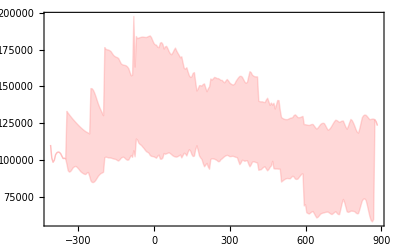

```mathematica
AllSamplAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[4]],{mm,1,6}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAreaAvTab[[ii]][[1]],AllSamplAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAreaAvTab]}]
```

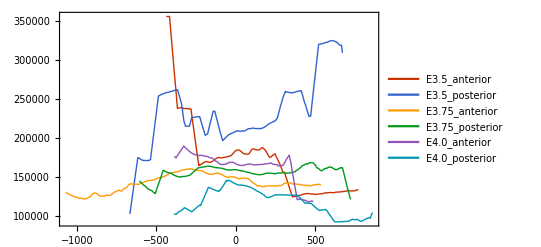

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Area/Area_"<>ToString[TabDevStage[[i]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,Length[TabDevStage]}];
```

### Aspect Ratio

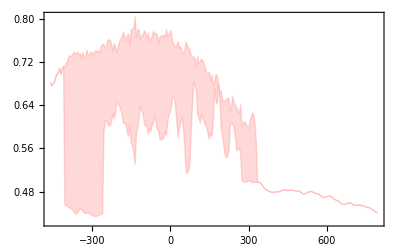
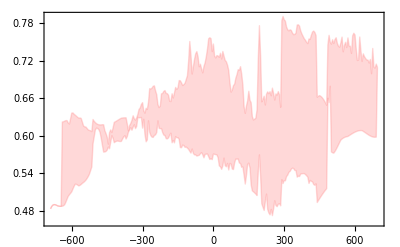
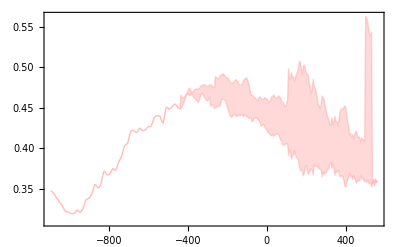
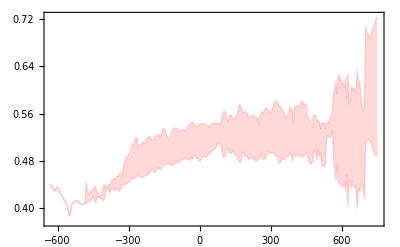
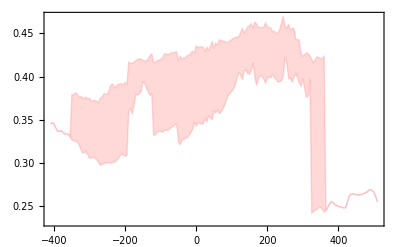
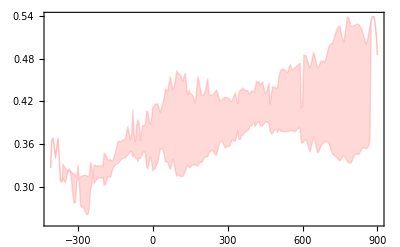

```mathematica
AllSamplAspAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[5]],{mm,1,6}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAspAvTab[[ii]][[1]],AllSamplAspAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAspAvTab]}]
```

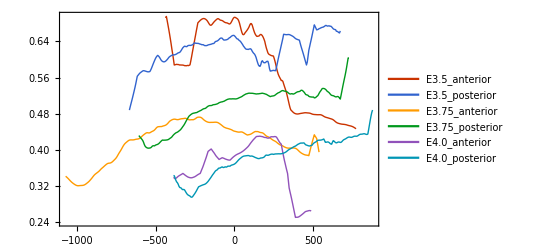

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAspAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplAspAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/AspectRatio/AspectRatio_"<>ToString[TabDevStage[[i]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAspAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAspAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,Length[TabDevStage]}];
```

### Len/Area

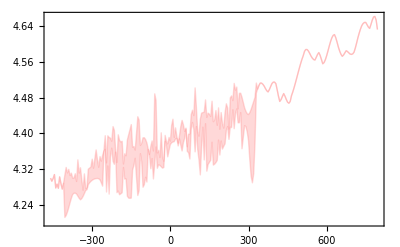
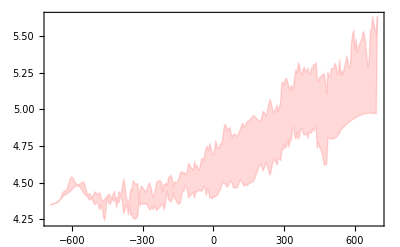
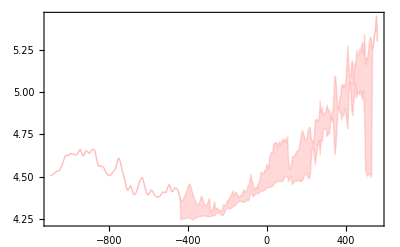
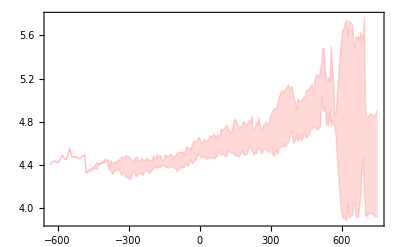
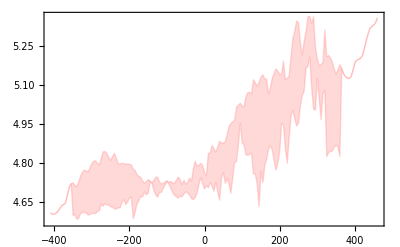
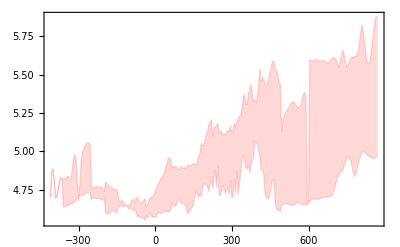

```mathematica
AllSamplLenAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[6]],{mm,1,6}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplLenAreaAvTab[[ii]][[1]],AllSamplLenAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplLenAreaAvTab]}]
```

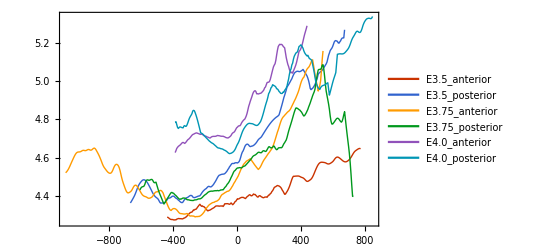

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplLenAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplLenAreaAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/LengthOverArea/LengthOverArea_"<>ToString[TabDevStage[[i]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,Length[TabDevStage]}];
```

### Curvature

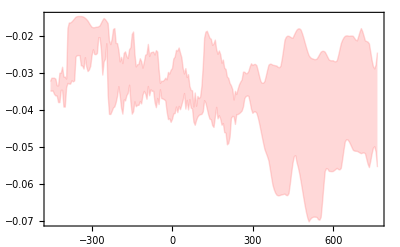
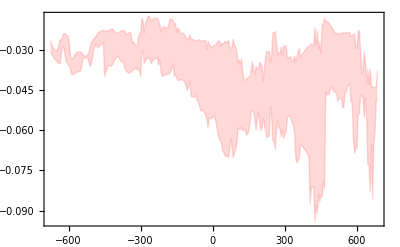
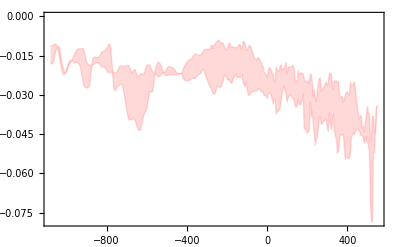
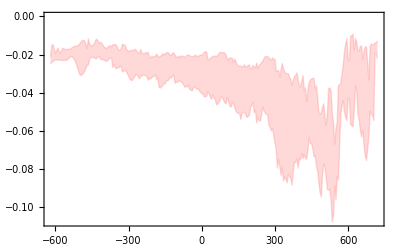
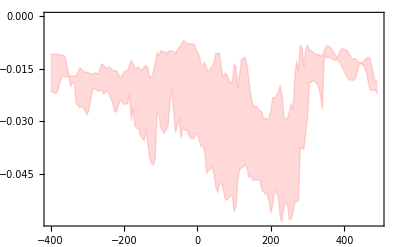
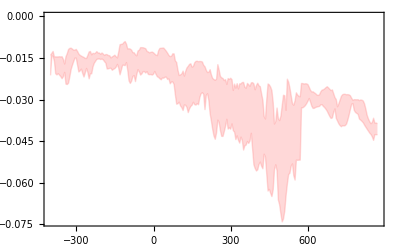

```mathematica
AllSamplCurvAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[1]],{mm,1,6}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplCurvAvTab[[ii]][[1]],AllSamplCurvAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplCurvAvTab]}]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Curv/MinCurv_"<>ToString[TabDevStage[[i]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplCurvAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplCurvAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,Length[TabDevStage]}];
```

### Shape characterization of outline through moments and width/height

```mathematica
(*Functions to import moments and width + height of outline of wilde type samples for each developmental stage*)MomentsWTOnly[TabData_,TabDevStage_,mm_,SelectString_,IgnoreCases_:{}]:=Module[{IndDevStage,LegendList,momentdata,TransFrame,LengthStep,tabmoments},IndDevStage=Table[DeleteElements[Flatten@Position[MapThread[And,{StringContainsQ[TabData[[All,1]],ToString[TabDevStage[[i]]]],StringContainsQ[TabData[[All,6]],SelectString]}],True],IgnoreCases],{i,1,Length[TabDevStage]}][[mm]];LegendList=Table[StringDrop[StringCases[TabData[[i,1]],"20"~~__~~"-"~~__~~"-"][[1]],-1],{i,IndDevStage}];
tabmoments=Table[momentdata=Import[TabData[[ii,1]]<>"/Outline_Outside_Coords/moments.txt","CSV"];
momentdata=Table[ToExpression[StringJoin[{"{",StringReplace[momentdata[[i]],"	"->","][[1]],"}"}]],{i,1,Length[momentdata]}];TransFrame=ToExpression[TabData[[ii,5]]];LengthStep=TabData[[mm,4]];momentdata[[TransFrame]],{ii,IndDevStage}];tabmoments[[All,{2,6}]]/tabmoments[[All,1]]^2]
WidthHeightWTOnly[TabData_,TabDevStage_,mm_,SelectString_,IgnoreCases_:{}]:=Module[{IndDevStage,LegendList,propdata,TransFrame,LengthStep,tabprop},IndDevStage=Table[DeleteElements[Flatten@Position[MapThread[And,{StringContainsQ[TabData[[All,1]],ToString[TabDevStage[[i]]]],StringContainsQ[TabData[[All,6]],SelectString]}],True],IgnoreCases],{i,1,Length[TabDevStage]}][[mm]];LegendList=Table[StringDrop[StringCases[TabData[[i,1]],"20"~~__~~"-"~~__~~"-"][[1]],-1],{i,IndDevStage}];
tabprop=Table[propdata=Import[TabData[[ii,1]]<>"/Outline_Outside_Coords/Properties.txt","CSV"];
propdata=Table[ToExpression[StringJoin[{"{",StringReplace[propdata[[i]],"	"->","][[1]],"}"}]],{i,1,Length[propdata]}];TransFrame=ToExpression[TabData[[ii,5]]];LengthStep=TabData[[mm,4]];propdata[[TransFrame]],{ii,IndDevStage}];tabprop[[All,{3,4}]]/Sqrt[tabprop[[All,7]]]]
```

```mathematica
(*Import moments and widht + height using above functions*)
momtab=Table[MomentsWTOnly[TabData,TabDevStage,i,"Yes",If[i==3,{124},{}]],{i,1,Length[TabDevStage]}];
```

```mathematica
widthheighttab=Table[WidthHeightWTOnly[TabData,TabDevStage,i,"Yes",If[i==3,{124},{}]],{i,1,Length[TabDevStage]}];
```

```mathematica
(*Export above data to csv file*)
Export["momtab.csv",momtab,"CSV"]
```

momtab.csv

Below some plots characterizing the shape for the different developmental stages

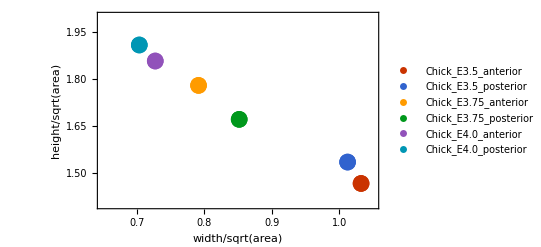

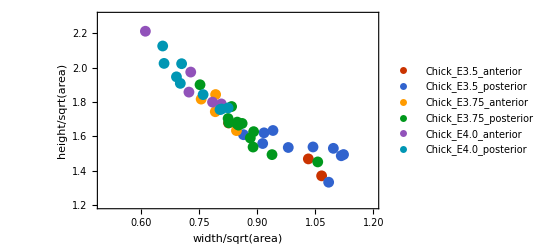

```mathematica
lpwh=ListPlot[Table[{Median[widthheighttab[[i]]]},{i,1,Length[widthheighttab]}],PlotRange->{{0.65,1.05},{1.4,2.}},PlotLegends->TabDevStage,FrameLabel->{"width/sqrt(area)","height/sqrt(area)"},PlotStyle->PointSize[0.03]]
p1=ListPlot[widthheighttab,PlotRange->{{0.5,1.2},{1.2,2.3}},PlotLegends->TabDevStage,FrameLabel->{"width/sqrt(area)","height/sqrt(area)"}]
```

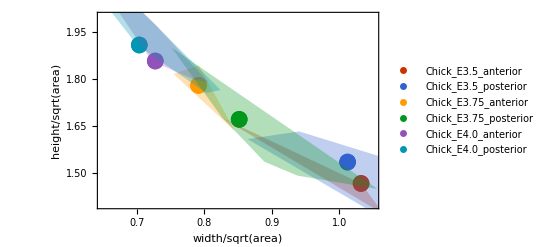

```mathematica
p2=Show[lpwh,Table[Graphics[{ColorData[112,"ColorList"][[i]],Opacity[0.3],ConvexHullMesh[widthheighttab[[i]]]}],{i,1,Length[widthheighttab]}]]
```

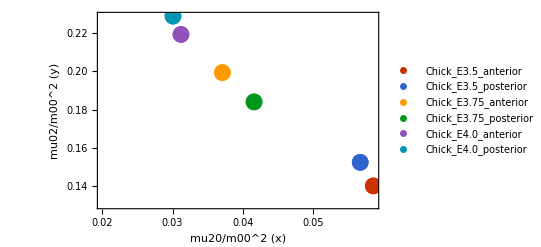

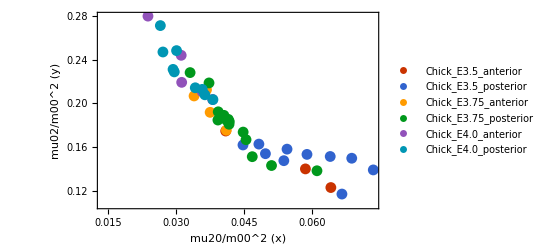

```mathematica
lpm=ListPlot[Table[{Median[momtab[[i]]]},{i,1,Length[momtab]}],PlotLegends->TabDevStage,FrameLabel->{"mu20/m00^2 (x)","mu02/m00^2 (y)"},PlotStyle->PointSize[0.03]]
p3=ListPlot[momtab,PlotRange->Full,PlotLegends->TabDevStage,FrameLabel->{"mu20/m00^2 (x)","mu02/m00^2 (y)"}]
```

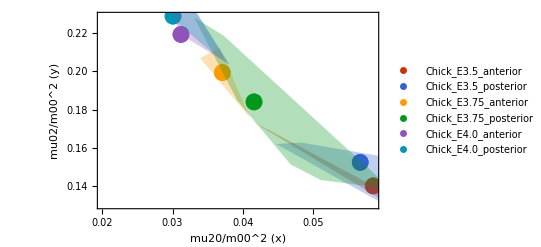

```mathematica
p4=Show[lpm,Table[Graphics[{ColorData[112,"ColorList"][[i]],Opacity[0.3],ConvexHullMesh[momtab[[i]]]}],{i,1,Length[momtab]}]]
```

## PF573228

```mathematica
TypeString="PF573228"
```

PF573228

### Width

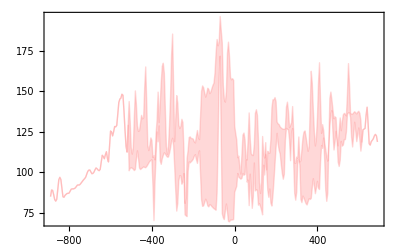
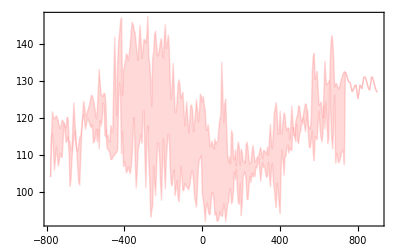

```mathematica
AllSamplWidthAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{47,58}][[2]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplWidthAvTab[[ii]][[1]],AllSamplWidthAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplWidthAvTab]}]
```

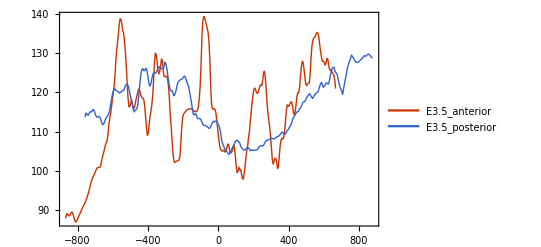

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplWidthAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Width/Width_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplWidthAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplWidthAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Height

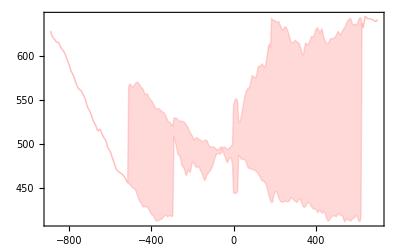
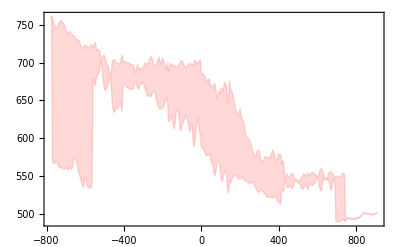

```mathematica
AllSamplHeightAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{47,58}][[3]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplHeightAvTab[[ii]][[1]],AllSamplHeightAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplHeightAvTab]}]
```

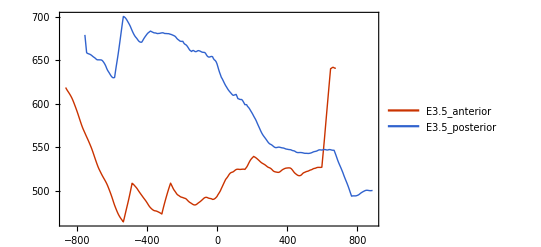

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplHeightAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Height/Height_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplHeightAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplHeightAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Area

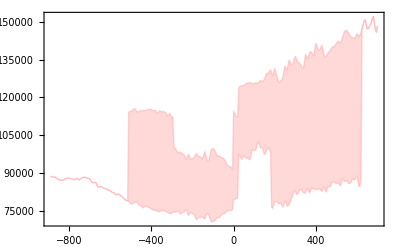
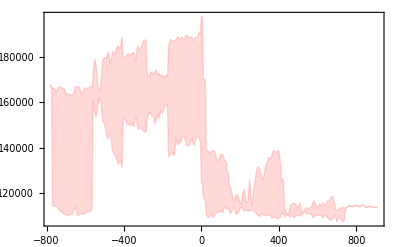

```mathematica
AllSamplAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{47,58}][[4]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAreaAvTab[[ii]][[1]],AllSamplAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAreaAvTab]}]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Area/Area_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Aspect Ratio

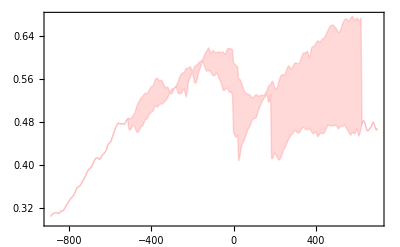
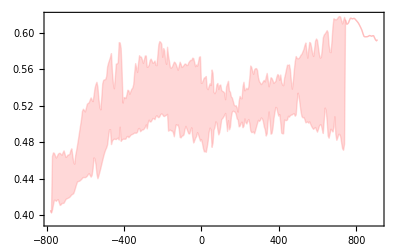

```mathematica
AllSamplAspAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{47,58}][[5]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAspAvTab[[ii]][[1]],AllSamplAspAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAspAvTab]}]
```

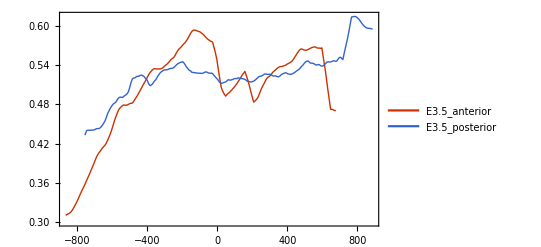

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAspAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplAspAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/AspectRatio/AspectRatio_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAspAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAspAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Len/Area

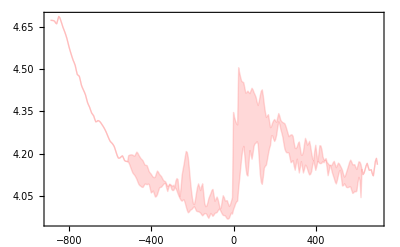
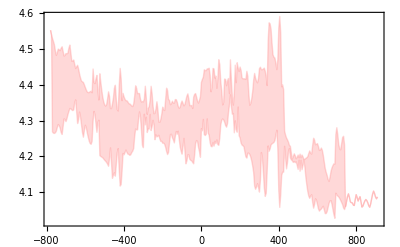

```mathematica
AllSamplLenAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{47,58}][[6]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplLenAreaAvTab[[ii]][[1]],AllSamplLenAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplLenAreaAvTab]}]
```

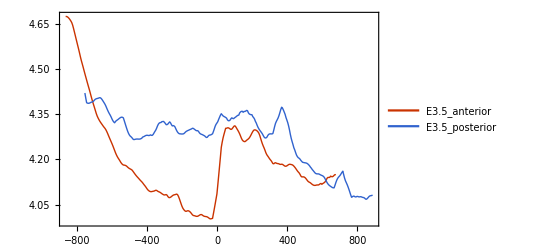

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplLenAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplLenAreaAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/LengthOverArea/LengthOverArea_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Curvature

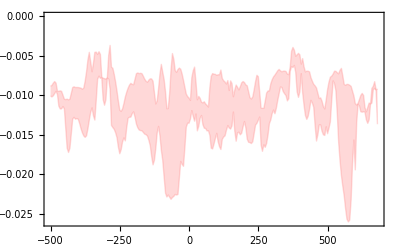
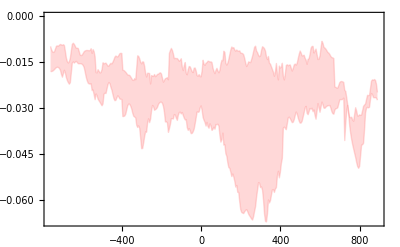

```mathematica
AllSamplCurvAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{47,58}][[1]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplCurvAvTab[[ii]][[1]],AllSamplCurvAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplCurvAvTab]}]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Curv/MinCurv_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplCurvAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplCurvAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

## Shh inhibition

```mathematica
TypeString="Shh inhibition"
```

Shh inhibition

### Width

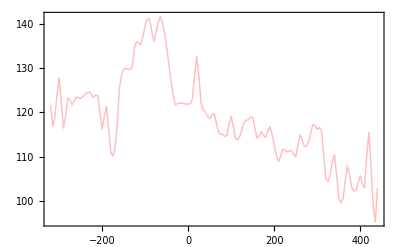
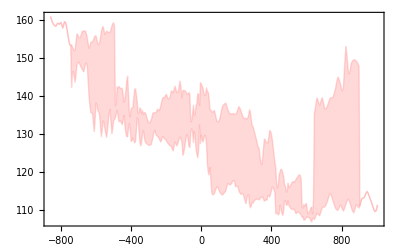

```mathematica
AllSamplWidthAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{62,76}][[2]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplWidthAvTab[[ii]][[1]],AllSamplWidthAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplWidthAvTab]}]
```

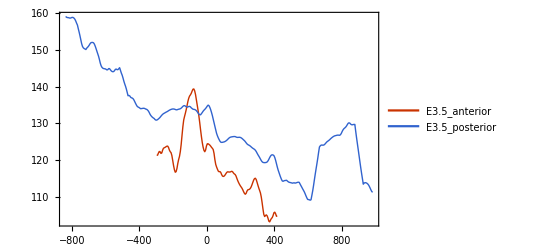

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplWidthAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Width/Width_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplWidthAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplWidthAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Height

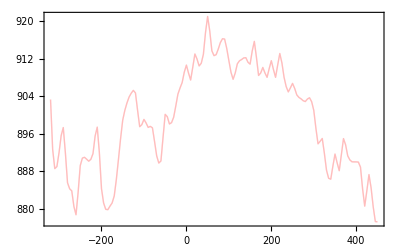
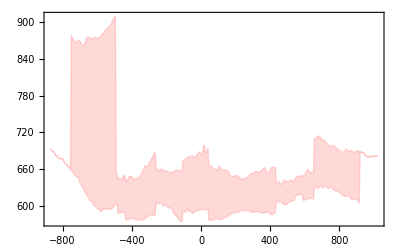

```mathematica
AllSamplHeightAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{62,76}][[3]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplHeightAvTab[[ii]][[1]],AllSamplHeightAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplHeightAvTab]}]
```

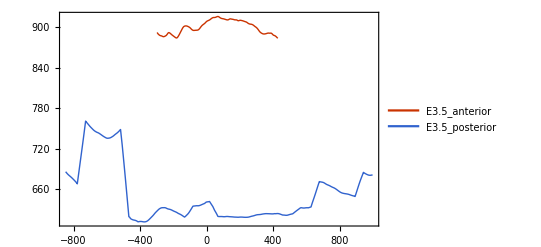

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplHeightAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Height/Height_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplHeightAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplHeightAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Area

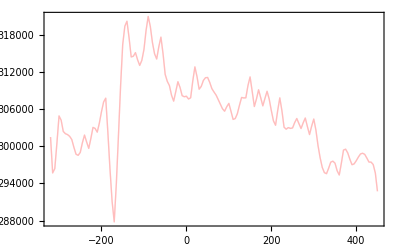
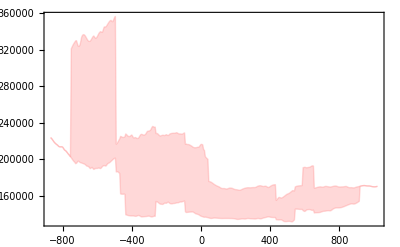

```mathematica
AllSamplAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{62,76}][[4]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAreaAvTab[[ii]][[1]],AllSamplAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAreaAvTab]}]
```

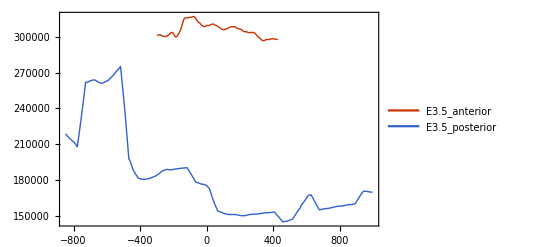

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Area/Area_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Aspect Ratio

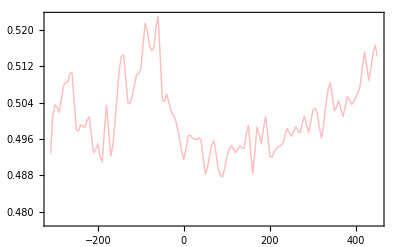
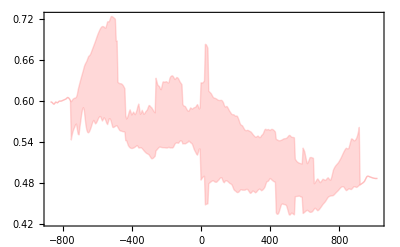

```mathematica
AllSamplAspAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{62,76}][[5]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAspAvTab[[ii]][[1]],AllSamplAspAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAspAvTab]}]
```

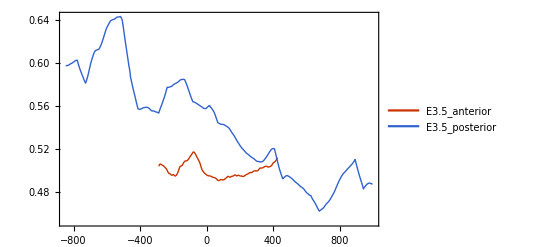

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAspAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplAspAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/AspectRatio/AspectRatio_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAspAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAspAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Len/Area

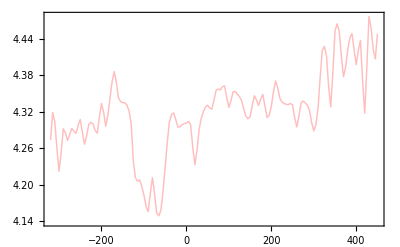
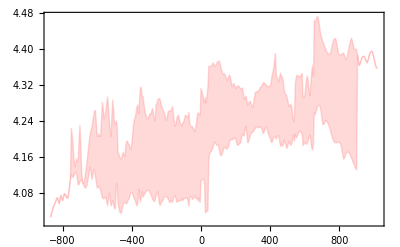

```mathematica
AllSamplLenAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{62,76}][[6]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplLenAreaAvTab[[ii]][[1]],AllSamplLenAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplLenAreaAvTab]}]
```

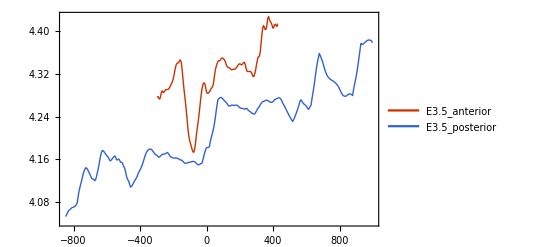

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplLenAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplLenAreaAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/LengthOverArea/LengthOverArea_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

### Curvature

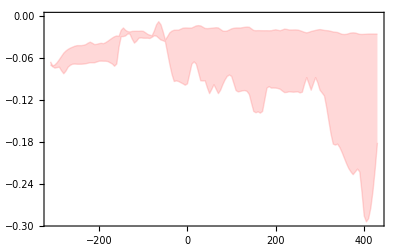
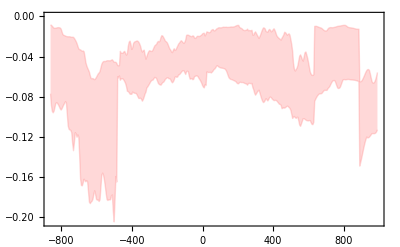

```mathematica
AllSamplCurvAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString,{62,76}][[1]],{mm,3,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplCurvAvTab[[ii]][[1]],AllSamplCurvAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplCurvAvTab]}]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Curv/MinCurv_"<>ToString[TabDevStage[[i+2]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplCurvAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplCurvAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,2}];
```

## Slightly reduced mesen. + compress

```mathematica
TypeString="Slightly reduced mes. + compress"
```

Slightly reduced mes. + compress

### Width

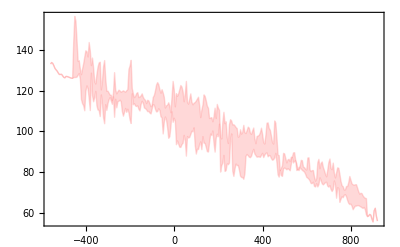

```mathematica
AllSamplWidthAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[2]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplWidthAvTab[[ii]][[1]],AllSamplWidthAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplWidthAvTab]}]
```

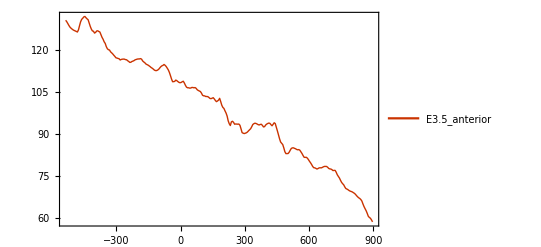

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplWidthAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Width/Width_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplWidthAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplWidthAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Height

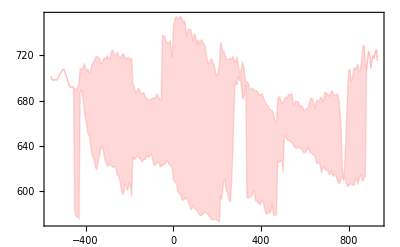

```mathematica
AllSamplHeightAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[3]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplHeightAvTab[[ii]][[1]],AllSamplHeightAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplHeightAvTab]}]
```

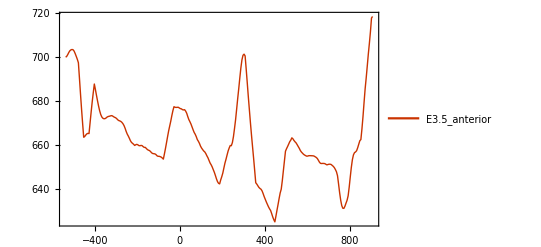

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplHeightAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Height/Height_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplHeightAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplHeightAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Area

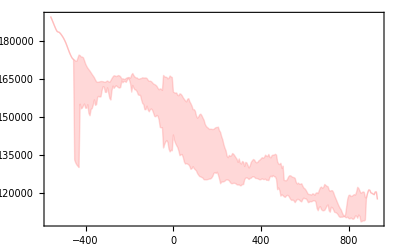

```mathematica
AllSamplAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[4]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAreaAvTab[[ii]][[1]],AllSamplAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAreaAvTab]}]
```

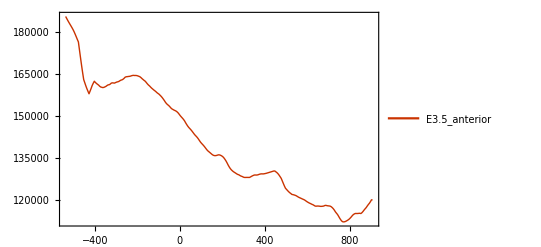

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Area/Area_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Aspect Ratio

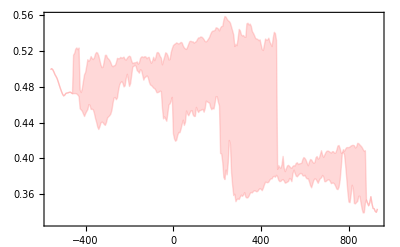

```mathematica
AllSamplAspAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[5]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAspAvTab[[ii]][[1]],AllSamplAspAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAspAvTab]}]
```

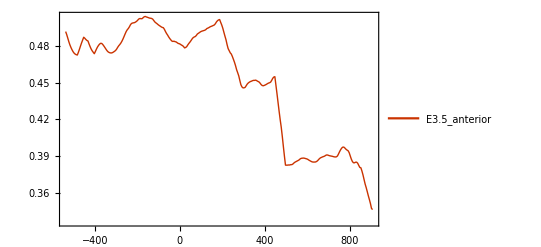

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAspAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplAspAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/AspectRatio/AspectRatio_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAspAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAspAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Len/Area

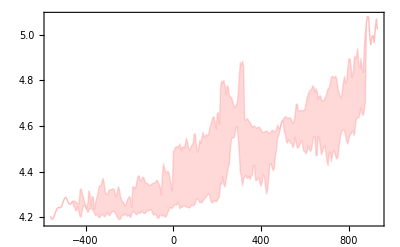

```mathematica
AllSamplLenAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[6]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplLenAreaAvTab[[ii]][[1]],AllSamplLenAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplLenAreaAvTab]}]
```

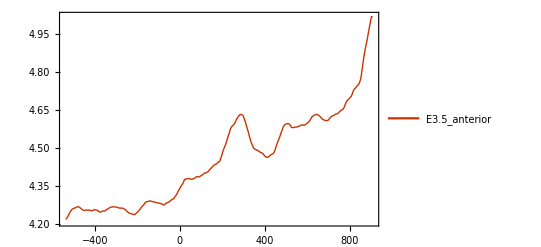

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplLenAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplLenAreaAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/LengthOverArea/LengthOverArea_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Curvature

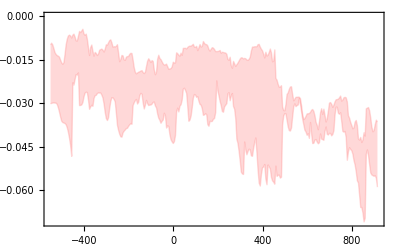

```mathematica
AllSamplCurvAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[1]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplCurvAvTab[[ii]][[1]],AllSamplCurvAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplCurvAvTab]}]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Curv/MinCurv_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplCurvAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplCurvAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

## Slightly reduced mesen.

```mathematica
TypeString="Slightly reduced mesen."
```

Slightly reduced mesen.

### Width

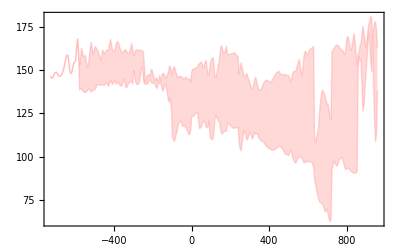

```mathematica
AllSamplWidthAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[2]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplWidthAvTab[[ii]][[1]],AllSamplWidthAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplWidthAvTab]}]
```

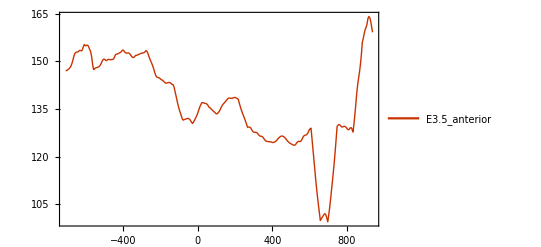

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplWidthAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Width/Width_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplWidthAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplWidthAvTab[[i]][[1]],AllSamplWidthAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplWidthAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Height

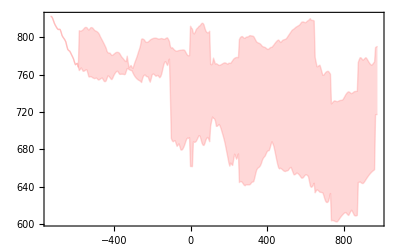

```mathematica
AllSamplHeightAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[3]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplHeightAvTab[[ii]][[1]],AllSamplHeightAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplHeightAvTab]}]
```

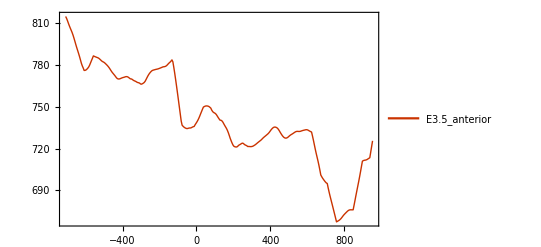

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplHeightAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Height/Height_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplHeightAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplHeightAvTab[[i]][[1]],AllSamplHeightAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplHeightAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Area

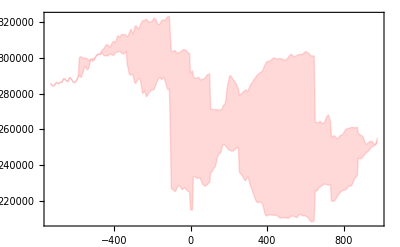

```mathematica
AllSamplAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[4]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAreaAvTab[[ii]][[1]],AllSamplAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAreaAvTab]}]
```

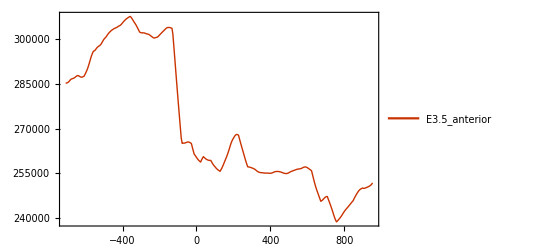

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplWidthAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Area/Area_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAreaAvTab[[i]][[1]],AllSamplAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Aspect Ratio

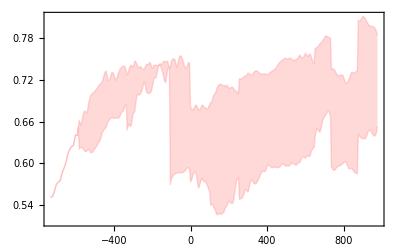

```mathematica
AllSamplAspAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[5]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplAspAvTab[[ii]][[1]],AllSamplAspAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplAspAvTab]}]
```

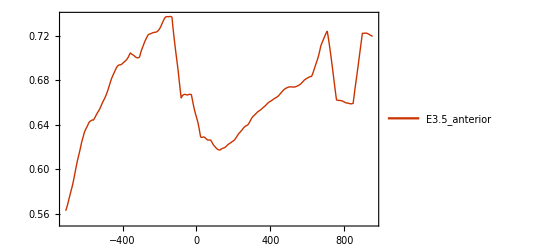

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplAspAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplAspAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/AspectRatio/AspectRatio_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplAspAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplAspAvTab[[i]][[1]],AllSamplAspAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplAspAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Len/Area

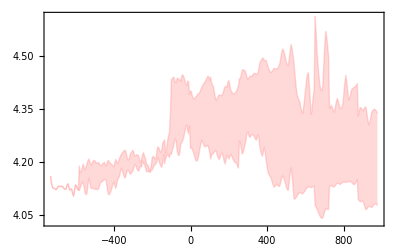

```mathematica
AllSamplLenAreaAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[6]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplLenAreaAvTab[[ii]][[1]],AllSamplLenAreaAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplLenAreaAvTab]}]
```

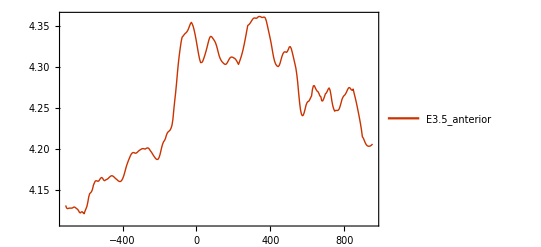

```mathematica
ListLinePlot[Table[MovingAverage[AllSamplLenAreaAvTab[[All,1]][[ii,All,1;;2]],10],{ii,1,Length[AllSamplLenAreaAvTab]}],PlotLegends->StringDrop[TabDevStage,6]]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/LengthOverArea/LengthOverArea_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplLenAreaAvTab[[i]][[1]],AllSamplLenAreaAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplLenAreaAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```

### Curvature

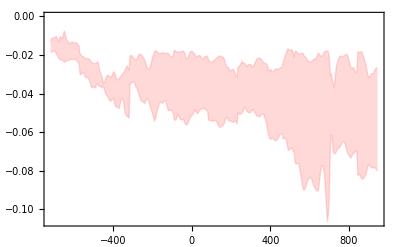

```mathematica
AllSamplCurvAvTab=Table[AverageSampleWTOnly[TabData,TabDevStage,mm,TypeString][[1]],{mm,4,4}];
VariationPlotTab=Table[ListLinePlot[VariationFunc[AllSamplCurvAvTab[[ii]][[1]],AllSamplCurvAvTab[[ii]][[2]]],PlotStyle->{{Pink,Opacity[0.3]},{Pink,Opacity[0.3]}},Filling->{1->{2}},FillingStyle->{Pink,Opacity[0.3]}],{ii,1,Length[AllSamplCurvAvTab]}]
```

```mathematica
Table[Export["Chick_Analysis/"<>TypeString<>"/Curv/MinCurv_"<>ToString[TabDevStage[[i+3]]]<>".csv",{Join[{"x value (time)"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,1]]],Join[{"Median"},AllSamplCurvAvTab[[All,1]][[All,All,1;;2]][[i]][[All,2]]],
Join[{"Median deviation upper"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[1,All,2]]],Join[{"Median deviation lower"},VariationFunc[AllSamplCurvAvTab[[i]][[1]],AllSamplCurvAvTab[[i]][[2]]][[2,All,2]]],Join[{"Number of samples averaged over"},AllSamplCurvAvTab[[All,1]][[All,All,1;;;;2]][[i]][[All,2]]]}],{i,1,1}];
```